Computational Dialogs in AP Calculus

Uhlman, Dan

Keane, Kyle

Taipei American School

Most representative image

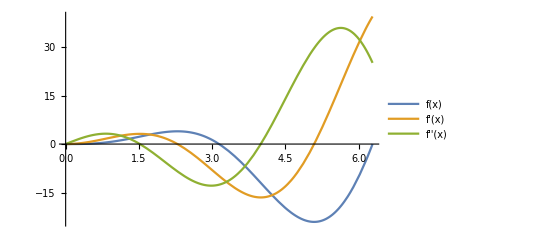

Abstract

GOAL OF THE PROJECT: Create homework assignments for AP Calculus AB that use Mathematica. Students will develop competency in both the Wolfram Language (WL) and differential calculus.

SUMMARY OF WORK: Nine assignments were created covering the core curriculum of differential calculus. The focus is on using Mathematica’s abilities to investigate and develop an understanding of calculus concepts. Students enter answers to questions in text cells and run code cells to investigate and check answers. Basic WL input is initially provided as a scaffold.

RESULTS AND FUTURE  WORK: The nine assignments cover the Definition of the Derivative, Differentiation Rules, Linear Motion, Trig Derivatives, The Chain Rule, Derivative Graphs, Implicit Differentiation, and derivatives of Inverse Trig, Exponential, and Logarithmic functions. Future work will include derivative applications such as optimization and related rates, and integral calculus.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

Get students using WL, once started, they will quickly outpace the teacher.

Topic Dialog format

Build WL skills to become resource for colleagues.

Expand to other courses in grades 8 - 12

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Nine notebooks were completed for differential calculus. Each notebook is written in the style of a topic exploration with short pieces of information, followed by a prompt to interact with a Manipulate output, examine a Plot, or answer a question. Cells are color-coded so students will know yellow cells require a text answer and blue cells require WL input and [shift] [enter] to run.

Code

Notebooks:

1 Definition of the Derivative:

https://github.com/DanUhlman/starthere/blob/master/1%20 Defn %20 of %20 Deriv %20 and %20 Diff.nb

2 Differentiation Rules:

https://github.com/DanUhlman/starthere/blob/master/2%20 Differentiation %20 Rules.nb

3 Linear Motion:

https://github.com/DanUhlman/starthere/blob/master/3%20 Linear %20 Motion_V2.nb

4 Trig Derivatives:

https://github.com/DanUhlman/starthere/blob/master/4%20 Trig %20 Derivs.nb

5 Chain Rule:

https://github.com/DanUhlman/starthere/blob/master/5%20 Chain %20 Rule.nb

6 Derivative Graphs:

https://github.com/DanUhlman/starthere/blob/master/6%20 Derivative %20 Graphs.nb

7 Implicit Differentiation:

https://github.com/DanUhlman/starthere/blob/master/7%20 Implicit %20 Diff.nb

8 Derivatives of Inverse Trig, Logs, and Exponential Functions:

https://github.com/DanUhlman/starthere/blob/master/8%20 Inv %20 Trig %20 Exp %20 Log %20 Derivs.nb

9 l’Hopital’s Rule

https://github.com/DanUhlman/starthere/blob/master/9%20 lHopitals %20 Rule.nb

Written Content / Lesson Plans

Prior to the first assignment (notebook), students will participate in a 10-minute teacher-guided Mathematica exploration using examples in the style of Stephen Wolfram’s Elementary Introduction to the Wolfram Language. This will focus on six main ideas:
1. [shift] [enter] to evaluate: 100! [shift] [enter]
2. Function names start with a capital letter: Pi, not pi
3. Square brackets for function arguments: Cos[Pi/6] or Solve[50 x^3-55 x^2==28x+3,x]
4. Curly braces for lists and ranges: Plot[4-x^2,{x,-3,3}]
5. = for W|A input: = Taiwan flag    or =size of Taiwan in square km
6. == for W|A output: == size of Taiwan

These assignments will replace the current pencil and paper homework that practice concepts after they were explained in class.

Since the assignments (notebooks) in this project allow students to investigate the calculus concepts prior to class, the face-to-face teaching time will be used to highlight questions about the concepts, focus on correct written notation, and explore connections and applications that the previous lesson model did not have time for.

Conclusions in Detail

Careful notes must be taken during the first implementation of these notebooks with students to see what they did not understand or had difficulty with. Each notebook will need to be modified using student feedback. The notebooks will also need to be evaluated for length. Each one has a target of 30 minutes for students to be able to complete. I would eventually like to target 45 minutes.

All Visualizations

Local Linearity:

```mathematica
g[x_]:=(0.5x)Sin[x];
Manipulate[
Plot[g[x],{x,2.5-zoom,2.5+zoom},PlotRange->{g[2.5]-.8zoom,g[2.5]+.2zoom},PlotLabel->"y=f(x)"],
{zoom,3,.01,-.01},SaveDefinitions->True]
```

Exploring patterns of rational exponents for derivative rules:

```mathematica
Manipulate[
TableForm[{x^p,D[x^p,x]}],
{p,0,10,1/2},"Function and its Derivative"
]
```

General::ivar: 1 is not a valid variable.

Explore average velocity vs. instantaneous velocity at t=1:

```mathematica
(* adapted from CalcLabs Mathematica 5e pg 60 (Hollis) *)
f[x_]:=3 x^2+1;
sec[h_][x_]:=f[1]+(f[1+h]-f[1])/h(x-1);
Manipulate[
Plot[{f[x],sec[h][x]},{x,0,4.5},PlotRange->{0,60},
Epilog->Point[{{1,f[1]},{1+h,f[1+h]}}],AxesLabel->{"t (sec)","s(t) (m)"}],{{h,3},.01,3,Appearance->"Labeled"},SaveDefinitions->True]
```

Exploring linear motion:

```mathematica
(* from CalcLabs Mathematica 5e pg 71 (Hollis) *)
s[t_]:=(t-2)^3-3t+9;
motion[positionf_,{t_,tmin_,tmax_},{htmin_,htmax_}]:=
Module[{track,ball,level,pt,grf,s,c,d},
s[tt_]:=positionf/.t->tt;
c=tmin-(tmax-tmin)/4;d=tmin-(tmax-tmin)/5;
track=Graphics[{Line[{{d,htmin},{d,htmax}}]}];
ball[y_]=Graphics[{PointSize[.033],Red,Point[{d,y}]}];
level[tt_,y_]=Graphics[{Line[{{d,y},{tt,y}}]}];
pt[tt_,y_]=Graphics[{PointSize[.02],Blue,Point[{tt,y}]}];
grf=Plot[s[t],{t,0,tmax},PlotStyle->Darker[Gray]];
Animate[Show[grf,track,
Plot[s[t],{t,tmin-.001,t2},PlotStyle->Thick],
Plot[Evaluate[s[t2]+s'[t2](t-t2)],{t,t2-d,t2+d},PlotStyle->Darker[Green]],level[t2,s[t2]],ball[s[t2]],
pt[t2,s[t2]],Ticks->{Range[Floor[tmin],tmax],Automatic},
AxesOrigin->Automatic,PlotRange->{{c,tmax},{htmin,htmax}},AxesLabel->{"t (sec)","s(t) (m)"}],{t2,tmin,tmax},SaveDefinitions->True,AnimationRunning->False]]
motion[s[t],{t,0,4.1},{-.5,8.5}]
```

Exploring the derivative of Sine:

```mathematica
f[x_]:=Sin[x]
tangent[f_,x0_,x_]:=f'[x0] (x-x0)+f[x0]
Manipulate[Plot[{f[x],tangent[f,p,x]},{x,0,2 π},PlotRange->{{0,2 π},{-3,3}},Epilog->{Red,PointSize[.015],Point@{p,f[p]},Darker[Green],PointSize[.03],Point@{p,f'[p]}}],{p,0,2 π},"f(x) = sin(x)",SaveDefinitions->True]
```

Exploring the derivative of Cosine:

```mathematica
f[x_]:=Cos[x]
tangent[f_,x0_,x_]:=f'[x0] (x-x0)+f[x0]
Manipulate[Plot[{f[x],tangent[f,p,x]},{x,0,2 π},PlotRange->{{0,2 π},{-3,3}},Epilog->{Red,PointSize[.015],Point@{p,f[p]},Darker[Green],PointSize[.03],Point@{p,f'[p]}}],{p,0,2 π},"g(x) = cos(x)",SaveDefinitions->True]
```

Investigating chain rule derivatives of nested functions:

```mathematica
TableForm[Table[{level,Nest[h,x,level]},{level,1,4}]]
```

1 | h(x)
2 | h(h(x))
3 | h(h(h(x)))
4 | h(h(h(h(x))))

```mathematica
Manipulate[D[Nest[h,x,level],x],{level,1,4,1},"Derivative of level (click the small '+')",SaveDefinitions->True]
```

General::ivar: 1 is not a valid variable.

Exploring derivative graphs:

```mathematica
f[x_]:=(1/3)x^3-x^2-3x+6;
Manipulate[Plot[{f[a]+f'[a]*(x-a),f[x]},{x,-3,5},PlotRange->{-5,8},PlotStyle->{Red,Blue},Epilog->{Red,PointSize[.015],Point@{a,f[a]}}
],{a,-2.2,4.5},SaveDefinitions->True]
```

Data Sources Links/References

Besides the fantastic face-to-face at Wolfram Summer School 2017, especially with my mentor, Kyle Keane, the following references were very helpful:

Elementary Introduction to the Wolfram Language 2e, by Stephen Wolfram, 2015
	https://www.amazon.com/Elementary-Introduction-Wolfram-Language-Second/dp/1944183051/ref=sr_ 1_ 1?ie=UTF8&qid=1499261865&sr=8-1&keywords=elementary+introduction+to+the+wolfram+language

Hands-on Start to Mathematica, by Cliff Hastings, Kelvin Mischo, and Michael Morrison, 2015
	https://www.amazon.com/dp/1579550770?ref_=ams_ad _dp _asin _ 3

Calclabs with Mathematica 5e, by Selwyn Hollis, 2012
	https://www.amazon.com/CalcLabs-Mathematica-Single-Variable-Calculus/dp/0840058144/ref=sr_ 1_ 1?ie=UTF8&qid=1499262026&sr=8-1&keywords=calclabs+with+mathematica

Future Directions

Develop the same type of notebooks for derivative applications and integral calculus.

Background Info Links/References

Keywords

Calculus

AP Calculus

Derivative

High School

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```